{668.,742.,757.,732.,692.,662.,685.}

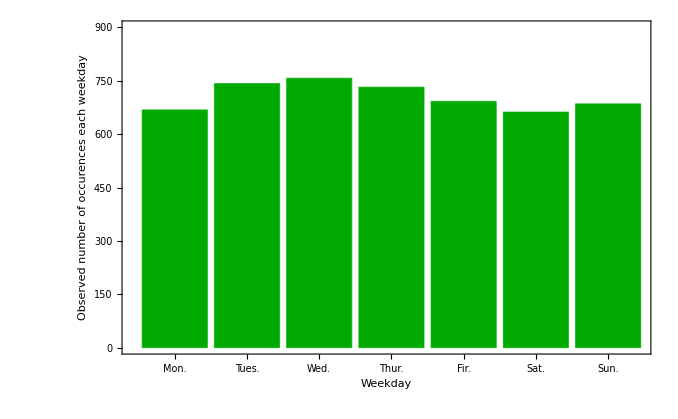

{442.,415.,458.,393.,376.,408.,439.,418.,363.,411.,392.,423.}

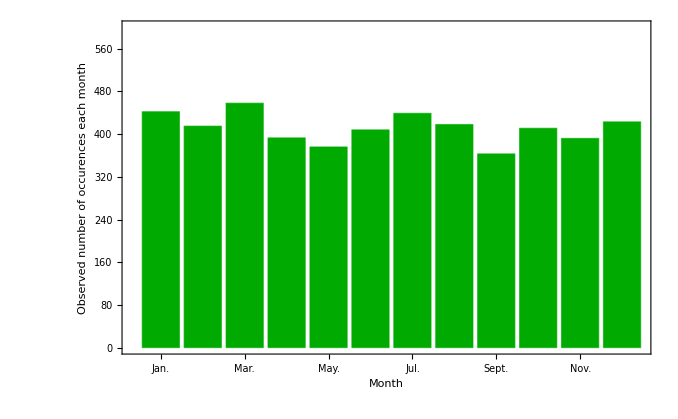

```mathematica
SetDirectory[NotebookDirectory[]];
Week1 = OpenRead["Tim_weekday_15to19.txt"];
Week = ReadList[Week1,Number]

BarChart[Week, ChartStyle->Darker[Green], ChartLabels->{"Mon.","Tues.","Wed.","Thur.","Fir.","Sat.","Sun."},Frame->{True,True,True,True},FrameLabel->{Style["Weekday",Black,16],Style["Observed number of occurences each weekday",Black,16]},LabelStyle->{Black,14},PlotRange->{0,900}]
Mon1 = OpenRead["Tim_month_15to19.txt"];
Mon = ReadList[Mon1,Number]

BarChart[Mon,ChartStyle->Darker[Green], ChartLabels->{"Jan.","Feb.","Mar.","Apr.","May.","Jun.","Jul.","Aug.","Sept.", "Oct.","Nov.","Dec."},Frame->{True,True,True,True},FrameLabel->{Style["Month",Black,16],Style["Observed number of occurences each month",Black,16]},LabelStyle->{Black,14},PlotRange->{0,600}]
```